```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[{"/home/will/Documents/MSc. AMTP/Thesis/ReggeWheeler/"}];
```

```mathematica
<<ReggeWheeler`
```

```mathematica
solMe =With[{a=0.,r0=10.`64,e=0,x=1, s=2,l=2,m=2,n=0},
orbit=KerrGeoOrbit[a,r0,e,x];
modeMe=ReggeWheelerPointParticleMode[s,l,m,n,orbit,Method->{"Hyperboloidal","GridPoints"->64}]
]
```

ReggeWheelerMode[…]

```mathematica
solMe["EnergyFlux"]
```

<|ℐ→0.00002684397739551056801050367238315917,ℋ→5.654138734536942973333079049173945×10^-9|>

```mathematica
ReggeWheeler`Hyperboloidal`Private`necessaryMinPrecision[orbit["p"],2,1]
```

26.

```mathematica
solMe["RadialFunction"][11]
```

0.01374527685048798572239085335004070928+3.51159368926239177×10^-21 ⅈ

```mathematica
solMe["EnergyFlux"]
```

<|ℐ→1.645681474579471970483378317×10^-23,ℋ→3.675597659530920186072554759×10^-23|>

```mathematica
solTkt = With[{a=0.,r0=2000.`64,e=0,x=1, s=2,l=20,m=12,n=0},
orbit=KerrGeoOrbit[a,r0,e,x];
modeTkt=ReggeWheelerPointParticleMode[s,l,m,n,orbit]
]
```

ReggeWheelerMode[…]

```mathematica
solTkt["EnergyFlux"]
```

<|ℐ→2.7407819862565457299748145927044645474671397072848×10^-81,ℋ→1.0995392367703316276665051369280111364671747877175×10^-159|>

```mathematica
solMe["Amplitudes"]
```

<|ℐ→-0.457499687527620942133877262470813299+0.1248263395913423566883027980384227 ⅈ,ℋ→0.006335118286860198621347092342346987-0.002689661351723081890541582443189867 ⅈ|>

```mathematica
solTkt["Amplitudes"]
```

<|ℐ→-0.3431247656457157101824+0.09361975469350677334973 ⅈ,ℋ→0.005105006304635709957706-0.000763813914397858754557 ⅈ|>

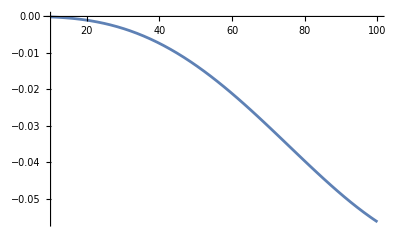

```mathematica
Plot[Im[solTkt["Amplitudes"][[1]]solTkt["RadialFunctions"]["Up"][r]],{r,10.01,100}]
```

```mathematica
dataMe = Table[Im[solMe["RadialFunction"][r]],{r,6,100,1}];
```

```mathematica
(* TODO: Cut ξs in flux section package to just be their formulae *)
```

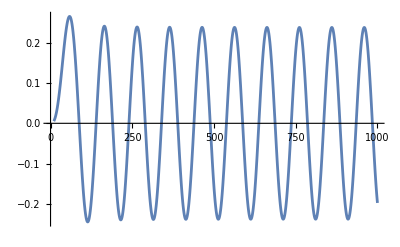

```mathematica
Plot[Im[solMe["RadialFunction"][r]],{r,10,1000},PlotRange->Automatic]
```

```mathematica
solTkt["Amplitudes"]
```

<|ℐ→-0.3431247656457157101824+0.09361975469350677334973 ⅈ,ℋ→0.005105006304635709957706-0.000763813914397858754557 ⅈ|>

```mathematica
solMe["Amplitudes"]
```

<|ℐ→0.45749968752088739885889128814-0.1248263395905670685072522522 ⅈ,ℋ→-0.0063351182860973135598622003+0.0026896613515670798976763323 ⅈ|>

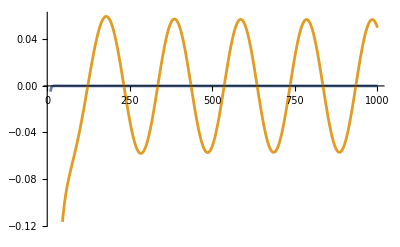

```mathematica
Plot[{Re[solMe["RadialFunction"][r]],Re[ampsTkt[[1]]*solTkt["RadialFunctions"]["Up"][r]]},{r,10,1000}]
```

```mathematica
ampsTkt[[1]]
```

0.05579645658583365055424-0.01109945783832491193897 ⅈ

```mathematica
solMe["Amplitudes"][[1]]
```

0.05579645658349974435757533746-0.01109945784421716816448096984 ⅈ

```mathematica
mode["Fluxes"]
```

<|Energy→<|ℐ→9.658046755396555063726327972×10^-8,ℋ→6.1345841572501801225849142×10^-10|>,AngularMomentum→<|ℐ→3.054142549545222598006939644×10^-6,ℋ→1.9399258434895108815115116×10^-8|>|>

```mathematica
?ReggeWheelerRadial
```

```mathematica
With[{a=0.`32,r0=10.`32,e=0,x=1, s=2,l=2,m=1,n=0},
orbit=KerrGeoOrbit[a,r0,e,x];
mode2=ReggeWheelerPointParticleMode[s,l,m,n,orbit]
]
```

ReggeWheelerMode[…]

```mathematica
mode2["Fluxes"]
```

<|Energy→<|ℐ→9.658046755783437928711×10^-8,ℋ→6.134584157264516968855×10^-10|>,AngularMomentum→<|ℐ→3.054142549667565702111×10^-6,ℋ→1.939925843494044590379×10^-8|>|>

```mathematica
1-(mode["EnergyFlux"][[2]])/(mode2["EnergyFlux"][[2]])
```

2.21776751584×10^-10

```mathematica
?ReggeWheelerHyperboloidal
```

```mathematica
Cos[π]
```

-1